## Ensure to open up and compile other files that are necessary to run the optimizations.

```mathematica
(* Some definitions for simplifying notation *)
kp[A_,B_]:= KroneckerProduct[A,B];

(* Anti-symmetric and symmetric structure constants for qutrits, commutator and anti-commutator of two operators, and the Gell-Mann Matrices with Identity *)
com[a_,b_]:= a.b - b.a;
aCom[a_,b_]:= a.b+b.a;

gm[0] = IdentityMatrix[3];
gm[1] = {{0,1,0},{1,0,0},{0,0,0}};
gm[2] = {{0,-I,0},{I,0,0},{0,0,0}};
gm[3] = {{1,0,0},{0,-1,0},{0,0,0}};
gm[4] = {{0,0,1},{0,0,0},{1,0,0}};
gm[5] = {{0,0,-I},{0,0,0},{I,0,0}};
gm[6] = {{0,0,0},{0,0,1},{0,1,0}};
gm[7] = {{0,0,0},{0,0,-I},{0,I,0}};
gm[8] = Divide[1,Sqrt[3]]{{1,0,0},{0,1,0},{0,0,-2}};
gmVec = {gm[1],gm[2],gm[3],gm[4],gm[5],gm[6],gm[7],gm[8]};

fStr[a_,b_,c_]:=-Divide[I,4]Tr[gm[a].com[gm[b],gm[c]]];
dStr[a_,b_,c_]:=Divide[1,4]Tr[gm[a].aCom[gm[b],gm[c]]];
gmMult[i_,j_]:= Divide[2,3]KroneckerDelta[i,j]IdentityMatrix[3] + Sum[(dStr[i,j,k]+I fStr[i,j,k])gm[k],{k,1,8}];
```

```mathematica
(* Partial transpose of a two-qutrit state (We give both the operational definition and the quantum channel that performs the equivalent transformation ) *)
channelTwoQutrit[state_]:= Divide[1,3] state+Divide[1,2](kp[gm[1],IdentityMatrix[3]].state.kp[gm[1],IdentityMatrix[3]]-kp[gm[2],IdentityMatrix[3]].state.kp[gm[2],IdentityMatrix[3]]+kp[gm[3],IdentityMatrix[3]].state.kp[gm[3],IdentityMatrix[3]]+kp[gm[4],IdentityMatrix[3]].state.kp[gm[4],IdentityMatrix[3]]-kp[gm[5],IdentityMatrix[3]].state.kp[gm[5],IdentityMatrix[3]]+kp[gm[6],IdentityMatrix[3]].state.kp[gm[6],IdentityMatrix[3]]-kp[gm[7],IdentityMatrix[3]].state.kp[gm[7],IdentityMatrix[3]]+kp[gm[8],IdentityMatrix[3]].state.kp[gm[8],IdentityMatrix[3]]);

partialTranspose[state_]:=Sum[First[{Flatten[kp[UnitVector[3,i],UnitVector[3,j]]]}.state.Flatten[kp[UnitVector[3,k],UnitVector[3,l]]]]Transpose[{Flatten[kp[UnitVector[3,k],UnitVector[3,j]]]}].{Flatten[kp[UnitVector[3,i],UnitVector[3,l]]]},{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
```

```mathematica
(* Definitions for creating the OO-invariant two-qutrit state *)
QMat[0] = Divide[1,2](kp[IdentityMatrix[3],IdentityMatrix[3]]+Sum[Transpose[{Flatten[kp[UnitVector[3,i],UnitVector[3,j]]]}].{Flatten[kp[UnitVector[3,j],UnitVector[3,i]]]},{i,1,3},{j,1,3}]);
QMat[1] = Divide[1,2](kp[IdentityMatrix[3],IdentityMatrix[3]]-Sum[Transpose[{Flatten[kp[UnitVector[3,i],UnitVector[3,j]]]}].{Flatten[kp[UnitVector[3,j],UnitVector[3,i]]]},{i,1,3},{j,1,3}]);
PMat[1] = Divide[1,3]Sum[Transpose[{Flatten[kp[UnitVector[3,i],UnitVector[3,i]]]}].{Flatten[kp[UnitVector[3,j],UnitVector[3,j]]]},{i,1,3},{j,1,3}];
ΠMat[0] = QMat[0] - PMat[1]; (* Symmetric state mixed with the maximally entangled state *)
ΠMat[1] = QMat[1]; (* Anti-symmetric state *)
ΠMat[2] = PMat[1]; (* Maximimally entangled state *)

(* The OO-invariant two-qutrit state dependent on the two parameters Subscript[π, 0] and Subscript[π, 1] *)
Clear[st];
st[π0_,π1_]:=π0 Divide[1,Tr[ΠMat[0]]]ΠMat[0]+π1 Divide[1,Tr[ΠMat[1]]]ΠMat[1]+(1-π0-π1)Divide[1,Tr[ΠMat[2]]]ΠMat[2];
```

```mathematica
(* The operator that swaps two arbitrary qutrits *)
qutritQutritSwap = Sum[Transpose[{Flatten[kp[UnitVector[3,i],UnitVector[3,j]]]}].{Flatten[kp[UnitVector[3,j],UnitVector[3,i]]]},{i,1,3},{j,1,3}];
```

```mathematica
(* Calculating the local objective function over the real vector space and simplifying according to normalization *)
(* This calculation is the inner product of the local state with respect to all real vectors *)
FullSimplify[{Flatten[kp[{a1,b1,c1},{d1,e1,f1}]]}.st[π0,π1].Flatten[kp[{a1,b1,c1},{d1,e1,f1}]],a1^2+b1^2+c1^2==1&&d1^2+e1^2+f1^2==1];
(* The simplified objective function we use for the "real" optimizations *)
localR[π0_,π1_]:=1/30 (10-6 π0+a1 c1 d1 f1 (20-18 π0-30 π1)-10 π1+e1^2 (-10+9 π0+15 π1)+f1^2 (-10+9 π0+15 π1)-2 b1 e1 (a1 d1+c1 f1) (-10+9 π0+15 π1)-b1^2 (-1+2 e1^2+f1^2) (-10+9 π0+15 π1)-c1^2 (-1+e1^2+2 f1^2) (-10+9 π0+15 π1));
(* Calculating the optimal value of the objective function "localR" over the normalization constraints using the "SimulatedAnnealing Method" *)
optLocalR[π0_,π1_]:= NMaximize[{localR[π0,π1],a1^2+b1^2+c1^2==1&&d1^2+e1^2+f1^2==1},{a1,b1,c1,d1,e1,f1},Method->"SimulatedAnnealing"];
```

```mathematica
(* Calculating the global objective function over the real vector space and simplifying according to normalization *)
(* The simplified expression is in the notebook file titled "OO_Invariant_State_Global_Objective_Function_for_Real_Optimization.nb" *)
FullSimplify[{Flatten[kp[{a1,b1,c1,d1,e1,f1,g1,h1,i1},{j1,k1,l1, m1,n1, o1, p1,q1,r1}]]}.KroneckerProduct[IdentityMatrix[3],qutritQutritSwap,IdentityMatrix[3]].kp[st[π0,π1],st[π0,π1]].Transpose[KroneckerProduct[IdentityMatrix[3],qutritQutritSwap,IdentityMatrix[3]]].Flatten[kp[{a1,b1,c1,d1,e1,f1,g1,h1,i1},{j1,k1,l1, m1,n1, o1, p1,q1,r1}]]//Expand,a1^2+b1^2+c1^2+d1^2+e1^2+f1^2+g1^2+h1^2+i1^2==1&&j1^2+k1^2+l1^2+m1^2+n1^2+o1^2+p1^2+q1^2+r1^2==1]
(* Calculating the optimal value of the objective function "globalR" over the normalization constraints using the "SimulatedAnnealing Method" *)
optGlobalR[π0_,π1_]:= NMaximize[{globalR[π0,π1],a1^2+b1^2+c1^2+d1^2+e1^2+f1^2+g1^2+h1^2+i1^2==1&&j1^2+k1^2+l1^2+m1^2+n1^2+o1^2+p1^2+q1^2+r1^2==1},{a1,b1,c1,d1,e1,f1,g1,h1,i1,j1,k1,l1,m1,n1,o1,p1,q1,r1},Method->"SimulatedAnnealing"];
```

```mathematica
(* Calculating the objective function over the complex vector space and simplifying according to normalization *)
(* This calculation is the inner product of the local state with respect to all complex vectors *)
FullSimplify[{Flatten[kp[{a1-I a2,b1-I b2,c1-I c2},{d1-I d2,e1-I e2,f1-I f2}]]}.st[π0,π1].Flatten[kp[{a1+I a2,b1+I b2,c1+I c2},{d1+I d2,e1+I e2,f1+I f2}]],a1^2+a2^2+b1^2+b2^2+c1^2+c2^2==1&&d1^2+d2^2+e1^2+e2^2+f1^2+f2^2==1];
(* The simplified objective function we use for the "complex" optimizations *)
localC[π0_,π1_]:=1/30 (10-6 π0+a1 c1 d1 f1 (20-18 π0-30 π1)+a2 c2 d1 f1 (20-18 π0-30 π1)+c1^2 f1^2 (20-18 π0-30 π1)+c2^2 f1^2 (20-18 π0-30 π1)+a1 c1 d2 f2 (20-18 π0-30 π1)+a2 c2 d2 f2 (20-18 π0-30 π1)+c1^2 f2^2 (20-18 π0-30 π1)+c2^2 f2^2 (20-18 π0-30 π1)+c1^2 e1^2 (10-9 π0-15 π1)+c2^2 e1^2 (10-9 π0-15 π1)+c1^2 e2^2 (10-9 π0-15 π1)+c2^2 e2^2 (10-9 π0-15 π1)-10 π1+10 a2 c1 d2 f1 (-2+3 π0+π1)-10 a1 c2 d2 f1 (-2+3 π0+π1)-10 a2 c1 d1 f2 (-2+3 π0+π1)+10 a1 c2 d1 f2 (-2+3 π0+π1)+c1^2 (-10+9 π0+15 π1)+c2^2 (-10+9 π0+15 π1)+e1^2 (-10+9 π0+15 π1)+e2^2 (-10+9 π0+15 π1)+f1^2 (-10+9 π0+15 π1)+f2^2 (-10+9 π0+15 π1)-b1^2 (-1+2 e1^2+2 e2^2+f1^2+f2^2) (-10+9 π0+15 π1)-b2^2 (-1+2 e1^2+2 e2^2+f1^2+f2^2) (-10+9 π0+15 π1)+b1 (c1 e1 f1 (20-18 π0-30 π1)+c1 e2 f2 (20-18 π0-30 π1)+10 a2 (d2 e1-d1 e2) (-2+3 π0+π1)-10 c2 e2 f1 (-2+3 π0+π1)+10 c2 e1 f2 (-2+3 π0+π1)-2 a1 (d1 e1+d2 e2) (-10+9 π0+15 π1))+b2 (c2 e1 f1 (20-18 π0-30 π1)+c2 e2 f2 (20-18 π0-30 π1)-10 a1 (d2 e1-d1 e2) (-2+3 π0+π1)+10 c1 e2 f1 (-2+3 π0+π1)-10 c1 e1 f2 (-2+3 π0+π1)-2 a2 (d1 e1+d2 e2) (-10+9 π0+15 π1)));
(* Calculating the optimal value of the objective function "localC" over the normalization constraints using the "SimulatedAnnealing Method" *)
optLocalC[π0_,π1_]:= NMaximize[{localC[π0,π1],a1^2+a2^2+b1^2+b2^2+c1^2+c2^2==1&&d1^2+d2^2+e1^2+e2^2+f1^2+f2^2==1},{a1,a2,b1,b2,c1,c2,d1,d2,e1,e2,f1,f2},Method->"SimulatedAnnealing"];
```

```mathematica
(* Calculating the global objective function over the complex vector space and simplifying according to normalization *)
(* The simplified expression is in the notebook file titled "OO_Invariant_State_Global_Objective_Function_for_Complex_Optimization.nb" *)
FullSimplify[{Flatten[kp[{a1-I a2,b1-I b2,c1-I c2,d1-I d2,e1-I e2,f1-I f2,g1-I g2,h1-I h2,i1-I i2},{j1-I j2,k1-I k2,l1-I l2, m1-I m2,n1-I n2, o1-I o2, p1-I p2,q1-I q2,r1-I r2}]]}.KroneckerProduct[IdentityMatrix[3],qutritQutritSwap,IdentityMatrix[3]].kp[st[π0,π1],st[π0,π1]].Transpose[KroneckerProduct[IdentityMatrix[3],qutritQutritSwap,IdentityMatrix[3]]].Flatten[kp[{a1+I a2,b1+I b2,c1+I c2,d1+I d2,e1+I e2,f1+I f2,g1+I g2,h1+I h2,i1+I i2},{j1+I j2,k1+I k2,l1+I l2, m1+I m2,n1+I n2, o1+I o2, p1+I p2,q1+I q2,r1+I r2}]]//Expand,a1^2+a2^2+b1^2+b2^2+c1^2+c2^2+d1^2+d2^2+e1^2+e2^2+f1^2+f2^2+g1^2+g2^2+h1^2+h2^2+i1^2+i2^2==1&&j1^2+j2^2+k1^2+k2^2+l1^2+l2^2+m1^2+m2^2+n1^2+n2^2+o1^2+o2^2+p1^2+p2^2+q1^2+q2^2+r1^2+r2^2==1]
(* Calculating the optimal value of the objective function "globalC" over the normalization constraints using the "SimulatedAnnealing Method" *)
optGlobalC[π0_,π1_]:= NMaximize[{globalC[π0,π1],a1^2+a2^2+b1^2+b2^2+c1^2+c2^2+d1^2+d2^2+e1^2+e2^2+f1^2+f2^2+g1^2+g2^2+h1^2+h2^2+i1^2+i2^2==1&&j1^2+j2^2+k1^2+k2^2+l1^2+l2^2+m1^2+m2^2+n1^2+n2^2+o1^2+o2^2+p1^2+p2^2+q1^2+q2^2+r1^2+r2^2==1},{a1,a2,b1,b2,c1,c2,d1,d2,e1,e2,f1,f2,g1,g2,h1,h2,i1,i2,j1,j2,k1,k2,l1,l2,m1,m2,n1,n2,o1,o2,p1,p2,q1,q2,r1,r2},Method->"SimulatedAnnealing"];
```

```mathematica
(* We take the difference of the optimal values for the global and local states to determine if the multiplicative property holds. If it does not hold, then we get a positive real number. *)
(* Our threshold is set to 10^-5 to show a relevant violation. *)
pointsC[π0_,π1_]:=Chop[First[optGlobalC[π0,π1]]-First[optLocalC[π0,π1]]^2,10^-5];

(* We generate a table of points on the graph for the optimization over all complex vectors. The conditions in the "If" statements determine if the state is entangled for the given paramters Subscript[π, 0] and Subscript[π, 1]. *)
(* The PointSize is the same size for all states that do not lead to a violation of the multiplicative property. The size changes depending on how large the violation is. *)
coloredPointsC=Table[With[{value=pointsC[π0,π1]},{If[value<=0,If[1/30 (10-9 π0-5 π1)<0||1/3 (1-2 π1)<0||1/6 (-2+3 π0+3 π1)<0,Lighter[Blue],Green],If[1/30 (10-9 π0-5 π1)<0||1/3 (1-2 π1)<0||1/6 (-2+3 π0+3 π1)<0,Orange,Purple]],If[value>0,PointSize[2(-1/Log10[value])/100],PointSize[(2/3)0.02]],Point[{π0,π1}]}],{π0,0,1,0.025},{π1,0,1.001-π0,0.025}];

(* Flatten the points list *)
flattenedPointsC=Flatten[coloredPointsC,1];
(* Define the plot as "resultsR" *)
resultsC= Graphics[flattenedPointsC,Axes->True,AxesLabel->{"π0","π1"}]
(* Define the legend labels and colors *)
legendLabels={"Entangled and Violation","Separable and Violation","Entangled and No Violation","Separable and No Violation"};
legendColors={Orange,Purple,Blue,Green};
(* Create the legend *)
legend=SwatchLegend[legendColors,legendLabels];
(* Combine the graphic and the legend *)
Legended[resultsC,legend]
```

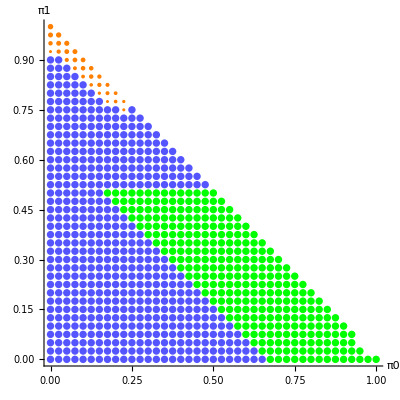

```mathematica
(* We take the difference of the optimal values for the global and local states to determine if the multiplicative property holds. If it does not hold, then we get a positive real number. *)
(* Our threshold is set to 10^-5 to show a relevant violation. *)
pointsR[π0_,π1_]:=Chop[First[optGlobalR[π0,π1]]-First[optLocalR[π0,π1]]^2,10^-5];
```

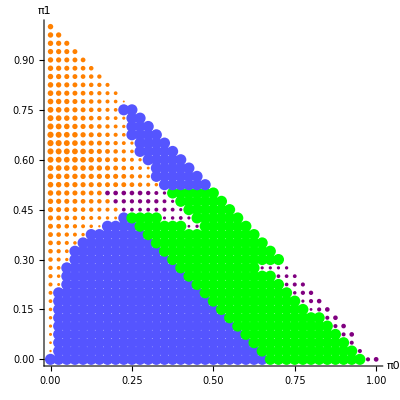

```mathematica
(* We generate a table of points on the graph for the optimization over all real vectors. The conditions in the "If" statements determine if the state is entangled for the given paramters Subscript[π, 0] and Subscript[π, 1]. *)
(* The PointSize is the same size for all states that do not lead to a violation of the multiplicative property. The size changes depending on how large the violation is. *)
coloredPointsR=Table[With[{value=pointsR[π0,π1]},{If[value<=0,If[1/30 (10-9 π0-5 π1)<0||1/3 (1-2 π1)<0||1/6 (-2+3 π0+3 π1)<0,Lighter[Blue],Green],If[1/30 (10-9 π0-5 π1)<0||1/3 (1-2 π1)<0||1/6 (-2+3 π0+3 π1)<0,Orange,Purple]],If[value>0,PointSize[2(-1/Log10[value])/100],PointSize[(2/3)0.02]],Point[{π0,π1}]}],{π0,0,1,0.025},{π1,0,1.001-π0,0.025}];

(* Flatten the points list *)
flattenedPointsR=Flatten[coloredPointsR,1];
(* Define the plot as "resultsR" *)
resultsR = Graphics[flattenedPointsR,Axes->True,AxesLabel->{"π0","π1"}]
(* Define the legend labels and colors *)
legendLabels={"Entangled and Violation","Separable and Violation","Entangled and No Violation","Separable and No Violation"};
legendColors={Orange,Purple,Blue,Green};
(* Create the legend *)
legend=SwatchLegend[legendColors,legendLabels];
(* Combine the graphic and the legend *)
Legended[resultsR,legend]
```

```mathematica
(* Additional check to show that both partial transpose definitions return the same separability criterion for the paramters Subscript[π, 0] and Subscript[π, 1] *)
```

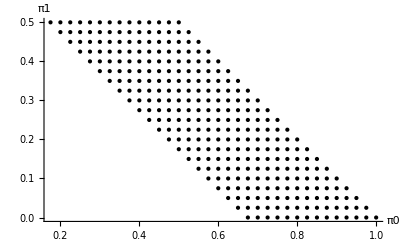

```mathematica
Graphics[Point /@ Flatten[Table[If[Min[Chop[Eigenvalues[channelTwoQutrit[st[π0,π1]]]]]≥0,{π0,π1},Nothing],{π0,0,1,0.025},{π1,0,1.001-π0,0.025}]//DeleteDuplicates,1],Axes->True,AxesLabel->{"π0","π1"}]
```

```mathematica
Graphics[Point /@ Flatten[Table[If[Min[Chop[Eigenvalues[partialTranspose[st[π0,π1]]]]]≥0,{π0,π1},Nothing],{π0,0,1,0.025},{π1,0,1.001-π0,0.025}]//DeleteDuplicates,1],Axes->True,AxesLabel->{"π0","π1"}]
```

-Graphics-